```mathematica
sim=Block[{i,data={},name0="Sim",name1=".csv"},For[i=1,i<=23,i++,AppendTo[data,Import["~/Work/ElektroShag/Data/Simul/"<>name0<>ToString[i]<>name1,"Table","FieldSeparators"->";"]]];data];
```

```mathematica
sim1=Import["~/Work/ElektroShag/Data/Simul/Sim1.csv","Table","FieldSeparators"->";"];
```

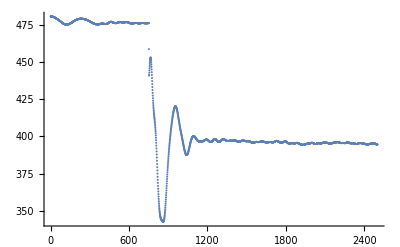

```mathematica
sim[[1]][[All,9]][[2;;]]//ListPlot
```

```mathematica
Delimiter
```

```mathematica
nodesN=Flatten[StringSplit[StringSplit[sim1[[1]][[2;;]],"_"][[All,1]],"N"],1];
```

```mathematica
StringSplit[sim1[[1]][[2;;]],"_"][[All,2]]
```

{f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,au,ai1,ai2,ai3,ai4,f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,i5,P5,Q5,i6,P6,Q6,au,ai1,ai2,ai3,ai4,ai5,ai6,f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,au,ai1,ai2,ai3,ai4,f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,i5,P5,Q5,au,ai1,ai2,ai3,ai4,ai5,f,r,u,i1,P1,Q1,au,ai1,f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,i5,P5,Q5,i6,P6,Q6,au,ai1,ai2,ai3,ai4,ai5,ai6,f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,au,ai1,ai2,ai3,ai4,f,r,u,i1,P1,Q1,i2,P2,Q2,au,ai1,ai2,f,r,u,i1,P1,Q1,au,ai1,f,r,u,i1,P1,Q1,i2,P2,Q2,i3,P3,Q3,i4,P4,Q4,au,ai1,ai2,ai3,ai4,f,r,u,i1,P1,Q1,i2,P2,Q2,au,ai1,ai2,f,r,u,i1,P1,Q1,i2,P2,Q2,au,ai1,ai2,f,r,u,i1,P1,Q1,au,ai1,f,r,u,i1,P1,Q1,au,ai1,f,r,u,i1,P1,Q1,au,ai1}

```mathematica
faza
```

{1,21,49,69,93,101,129,149,161,169,189,201,213,221,229}

```mathematica
faza=Flatten[Position[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],"f"],1];
Dfaza=Flatten[Position[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],"r"],1];
napetost=Flatten[Position[StringSplit[sim1[[1]][[2;;]],"_"][[All,2]],"u"],1];
```

```mathematica
sim[[1]][[2;;]][[All,faza]]
```

{{2017-01-01 00:00:00.000,-172.33,-35.7657,171.356,-39.2555,-21.8146,-68.5814,-72.8377,132.471,46.1511,-59.8854,7.98417,-41.9767,113.159,121.816},2498,{2017-01-01 00:00:49.980,-141.555,-7.96031,-144.69,7,40.5288,-6.22629,145.509,153.979}}
 |  |  |  |

```mathematica
napetost
```

{3,23,51,71,95,103,131,151,163,171,191,203,215,223,231}

```mathematica
Length@Table[sim[[All,1]][[All,i]],{i,Length[sim[[All,1]]]}]
```

23

```mathematica
sim[[1]]
```

{{Time,N1_f,N1_r,N1_u,N1_i1,N1_P1,N1_Q1,N1_i2,N1_P2,N1_Q2,N1_i3,N1_P3,N1_Q3,N1_i4,N1_P4,N1_Q4,205,N14_f,N14_r,N14_u,N14_i1,N14_P1,N14_Q1,N14_au,N14_ai1,N15_f,N15_r,N15_u,N15_i1,N15_P1,N15_Q1,N15_au,N15_ai1},2500}
 |  |  |  |